# Random Walk

-Graphics-

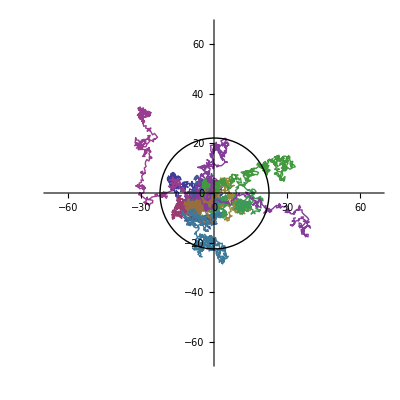

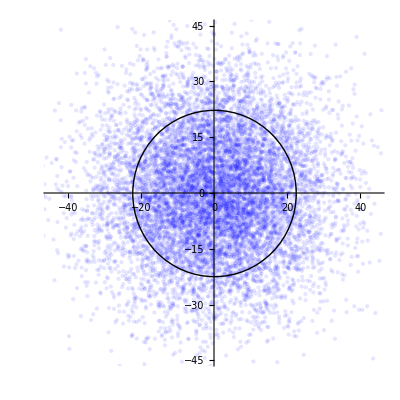

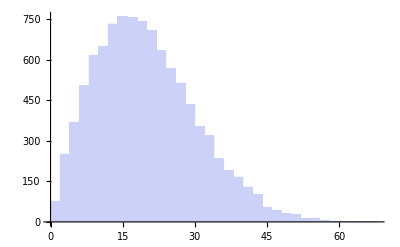

18.77

10.3684

22.3607

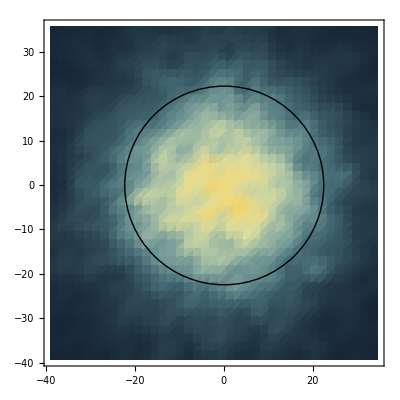

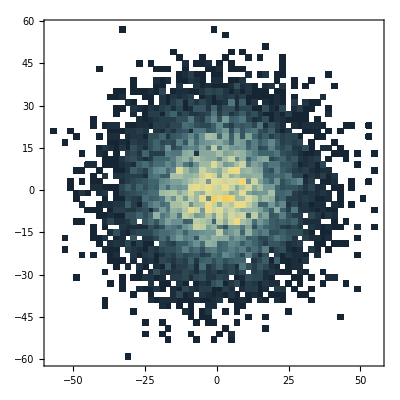

-Graphics3D-

```mathematica
Remove["Global`*"]
vector:=RandomReal[{-1,1},2]
walk[n_]:=FoldList[Plus,{0,0},{Cos[# π/180],Sin[# π/180]}&/@(RandomReal[{0,360},{n}])]
MakeVector[list_]:=Table[{list[[n-1]],list[[n]]},{n,2,Dimensions[list][[1]]}]
n=500;
w:=walk[n] ;
u=w;
Graphics[{(*Black,Line[u],*)Red,BSplineCurve[u,SplineDegree->10],Blue,BezierCurve[u,SplineDegree->10](*,Black,Point[u]*)}]
Show[ListLinePlot[Table[w,{i,1,10}],AxesOrigin->{0,0}],Graphics[Circle[{0,0},√n]],PlotRange->3{{-√n,√n},{-√n,√n}},AspectRatio->1]
samp=Table[w[[n+1]],{i,1,10000}];(*END POINTS OF WALK*)
Show[ListPlot[samp,AxesOrigin->{0,0},PlotRange->{{-2 √n,2 √n},{-2 √n,2 √n}},AspectRatio->1,PlotStyle->{{Opacity[.1],Blue,Thickness[.2]}}],Graphics[Circle[{0,0},√n]]]
Histogram[Table[Norm[samp[[i]]],{i,1,Dimensions[samp][[1]]}]]
dist=Norm/@samp;
Median[dist]
StandardDeviation[dist]
√n//N
Show[SmoothDensityHistogram[samp,1,ColorFunction->"StarryNightColors"],Graphics[Circle[{0,0},√n]]]
DensityHistogram[samp,ColorFunction->"StarryNightColors"]
SmoothHistogram3D[samp,ColorFunction->"StarryNightColors",Lighting->"Neutral"]
```